# Spontaneous Emission

### Compare Spontaneous Emission from either a projective monte-carlo simulation OR use density matrices

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Matthew\Documents\mnr_repos\Mathematica_Phys_Calculations\demonstration_notebooks

#### Rabi Flopping of 2-level atom

```mathematica
cg[δ_,Ω_,t_]:=(Cos[(√(δ^2+Ω^2)t)/2]-I δ/(√(δ^2+Ω^2))Sin[(√(δ^2+Ω^2))/2 t])Exp[I δ t/2]
ce[δ_,Ω_,t_]:=-I Ω/(√(δ^2+Ω^2))Sin[(√(δ^2+Ω^2)t)/2]Exp[-I δ t/2];
Pg[δ_,Ω_,t_]:=Abs[ce[δ,Ω,t]]^2 ;
```

```mathematica
Plot[{Abs[ce[0,1,t]]^2 },{t,0,π 6}];
```

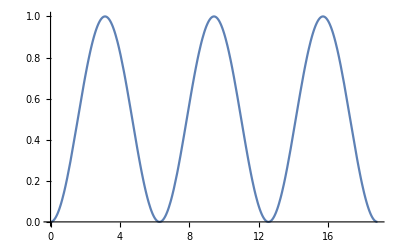

```mathematica
Plot[Pg[0,1,t],{t,0,π 6}]
```

#### Incoherent sum of rabi-flopping steps

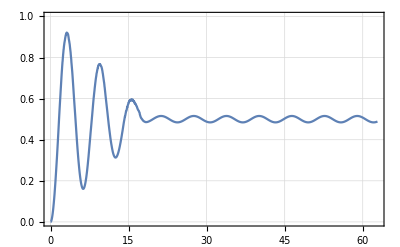

```mathematica
NN=350*2;
NR=RandomReal[1,NN] 6π;
Incoh[t_]:=Sum[If[t<NR⟦ii⟧,Pg[0,1,t],Pg[0,1,t-NR⟦ii⟧]],{ii,1,NN}]/NN
Plot[Incoh[t],{t,0,20π},
PlotRange-> {{0,20 π},{0,1}},
GridLines-> Automatic,
Frame-> True]
```

#### Compare individual snapshots of quantum jumps for a single-atom that is being driven by a alser

0.25

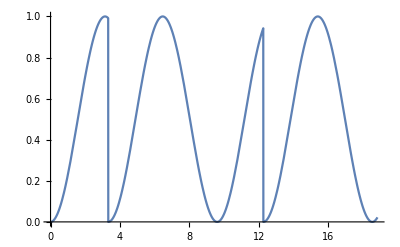
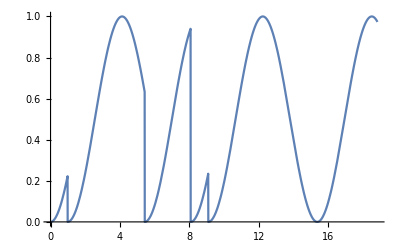
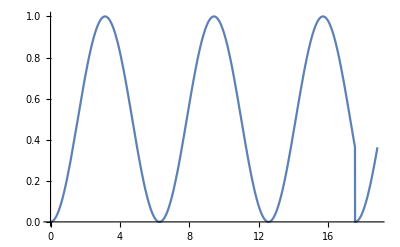
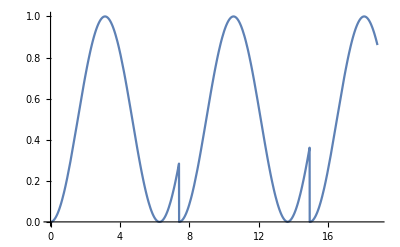
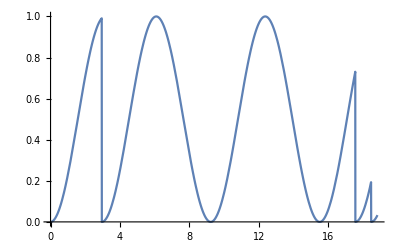
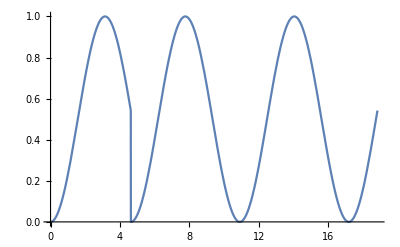
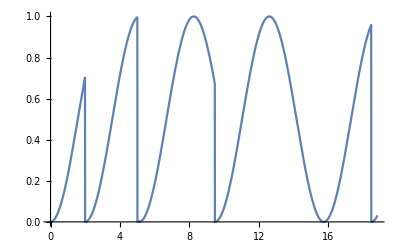
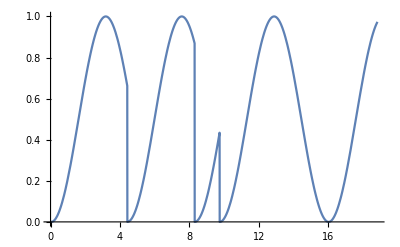

8Realizations.png

```mathematica
NN=50;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];

Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Plot[
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{t,0,6π}
]
,{jj,1,8}]
Export["8Realizations.png",%]
```

#### If we just add those small number of realizations together: 10 realizations

0.25

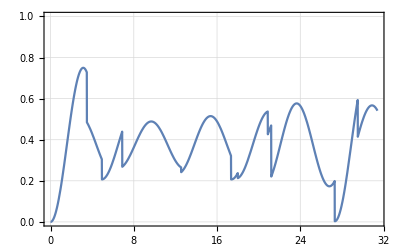

MonteCarloAvg10N.png

```mathematica
NN=10;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];


Incoh2[t_]:=Total[Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{jj,1,Length[TurnPoints]-1}]]/Length[TurnPoints]
MC10=Plot[Incoh2[t],{t,0,PlotTo},
PlotRange-> {{0,PlotTo},{0,1}},
GridLines-> Automatic,
Frame-> True]
Export["MonteCarloAvg10N.png",%]
```

```mathematica
NN=50;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];
```

#### Incoherent sum: 50 realizations

```mathematica
Incoh2[t_]:=Total[Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{jj,1,Length[TurnPoints]-1}]]/Length[TurnPoints]
MC50=Plot[Incoh2[t],{t,0,PlotTo},
PlotRange-> {{0,PlotTo},{0,1}},
GridLines-> Automatic,
Frame-> True]
Export["MonteCarloAvg50N.png",%]
```

#### Incoherent Sum : 250 realizations

0.25

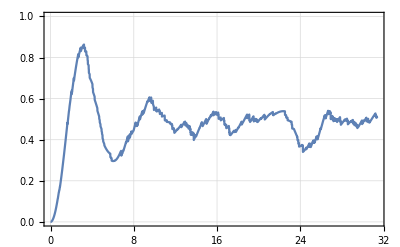

MonteCarloAvg250N.png

```mathematica
NN=250;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];


Incoh2[t_]:=Total[Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{jj,1,Length[TurnPoints]-1}]]/Length[TurnPoints]
MC250=Plot[Incoh2[t],{t,0,PlotTo},
PlotRange-> {{0,PlotTo},{0,1}},
GridLines-> Automatic,
Frame-> True]
Export["MonteCarloAvg250N.png",%]
```

#### Incoherent Sum: 1250 Realizations

0.25

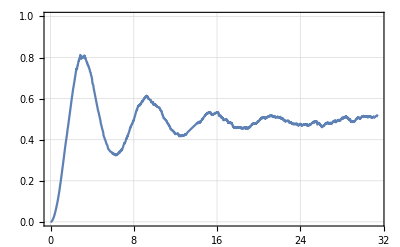

MonteCarloAvg1250N.png

```mathematica
NN=1250;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];


Incoh2[t_]:=Total[Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{jj,1,Length[TurnPoints]-1}]]/Length[TurnPoints]
MC1250=Plot[Incoh2[t],{t,0,PlotTo},
PlotRange-> {{0,PlotTo},{0,1}},
GridLines-> Automatic,
Frame-> True]
Export["MonteCarloAvg1250N.png",%]
```

#### Incoherent Sum 6000 Realizations

0.25

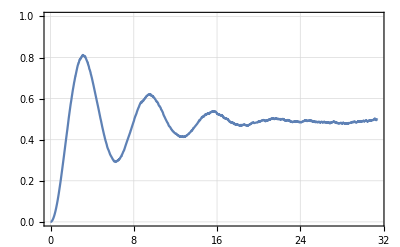

MonteCarloAvg6000N.png

```mathematica
NN=6000;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];


Incoh2[t_]:=Total[Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{jj,1,Length[TurnPoints]-1}]]/Length[TurnPoints]
MC6000=Plot[Incoh2[t],{t,0,PlotTo},
PlotRange-> {{0,PlotTo},{0,1}},
GridLines-> Automatic,
Frame-> True]
Export["MonteCarloAvg6000N.png",%]
```

#### Incoherent Sum 100,000 Realizations

0.25

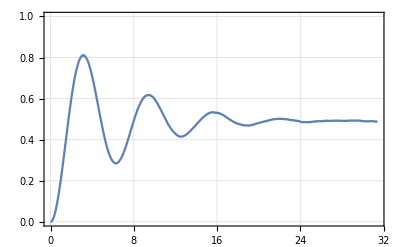

MonteCarloAvg100000N.png

```mathematica
NN=100000;
PlotTo=10π;
gamma=0.25
NR=RandomReal[1,NN] 5π;
Clear[NR]
NR=RandomVariate[ExponentialDistribution[gamma/2],NN];
NRN=Table[Total[NR⟦1;;ii⟧],{ii,1,Length[NR]}];
NRNMod=Mod[NRN,PlotTo];
NRNModM=NRNMod⟦2;;Length[NRN]⟧-NRNMod⟦1;;Length[NRN]-1⟧;
MVals=Select[NRNModM,#<0 &];
TurnPoints=Insert[
Append[
Flatten[
Table[Position[NRNModM,MVals⟦ii⟧],
{ii,1,Length[MVals]}]
],NN
],
0,
1];


Incoh2[t_]:=Total[Table[
SubNRN=N[Append[
Insert[NRNMod⟦TurnPoints⟦jj⟧+1;;TurnPoints⟦jj+1⟧⟧,0,1],
PlotTo
]];
Sum[
If[t>SubNRN⟦ii⟧,If[t< SubNRN⟦ii+1⟧,Pg[0,1,t-SubNRN⟦ii⟧],0],0]
,{ii,1,Length[SubNRN]-1}]
,{jj,1,Length[TurnPoints]-1}]]/Length[TurnPoints]
MC100000=Plot[Incoh2[t],{t,0,PlotTo},
PlotRange-> {{0,PlotTo},{0,1}},
GridLines-> Automatic,
Frame-> True]
Export["MonteCarloAvg100000N.png",%]
```

## Density Matrix Approach

#### This will be far faster and even more accurate in principle. But it is convincing to see the two approaches overlap.

100000.

1

0

0.25

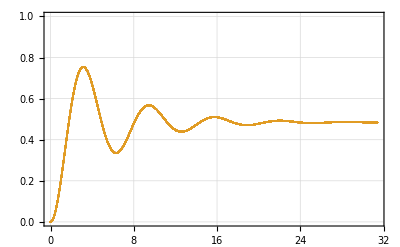

DensityMatrix.png

```mathematica
(*eqns={rgg'[t]== γ ree[t] + I/2(Ω reg[t] - rge[t]Ω),ree'[t]==-γ ree[t] + I/2(Ω rge[t] - Ω reg[t]),
rge'[t]==-(γ/2+I δ)rge[t]+ I/2 Ω (ree[t] - rgg[t]),
reg'[t]==-(γ/2-I δ)reg[t]+ I/2 Ω (ree[t] - rgg[t]),
rgg[0]=1,ree[0]==0};
*)
Clear[rgg,ree,reg,rge];
T=10 π;
dt=2π 0.00005;
RN=T/dt
rgg=Table[0,{ii,1,RN}];
ree=Table[0,{ii,1,RN}];
rge=Table[0,{ii,1,RN}];
reg=Table[0,{ii,1,RN}];
rgg⟦1⟧=1;
rgg⟦;;⟧;
Ω=1
δ=0
γ=gamma

For[ii=1,ii<RN,ii++,
rgg⟦ii+1⟧=(I Ω/2 rge⟦ii⟧ - I Ω/2 reg⟦ii⟧ + γ ree⟦ii⟧)dt+rgg⟦ii⟧;
ree⟦ii+1⟧=(I Ω/2 reg⟦ii⟧-I Ω/2 rge⟦ii⟧ - γ ree⟦ii⟧)dt+ree⟦ii⟧;
reg⟦ii+1⟧=(-I δ reg⟦ii⟧-I Ω/2(rgg⟦ii⟧-ree⟦ii⟧)-γ/2 reg⟦ii⟧)dt+reg⟦ii⟧;
rge⟦ii+1⟧=(I δ rge⟦ii⟧+I Ω/2(rgg⟦ii⟧-ree⟦ii⟧)-γ/2 rge⟦ii⟧)dt+rge⟦ii⟧;
]
reePlot=Table[{(ii-1) dt,ree⟦ii⟧},{ii,RN}];
linePlot=Table[{(ii-1)dt,0.5},{ii,RN}];
denseP=ListPlot[{reePlot},
PlotStyle-> {ColorData[97,"ColorList"]⟦2⟧,{Thin,Dashed,Black}},
PlotRange-> {{0,RN dt},{0,1}},
GridLines-> Automatic,
Frame-> True
]
Export["DensityMatrix.png",%]
```

## Comparison of Monte-Carlo to Finite Sampling of incoherent de-excitation average in rabi flopping

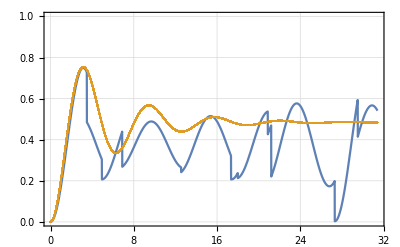

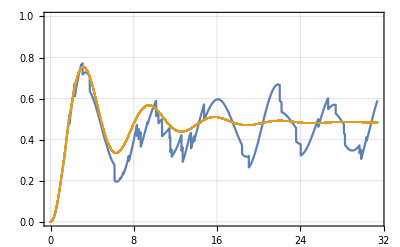

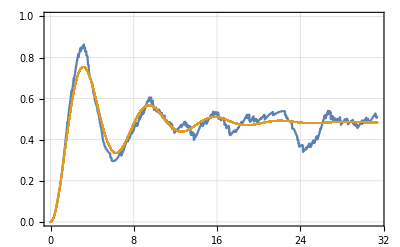

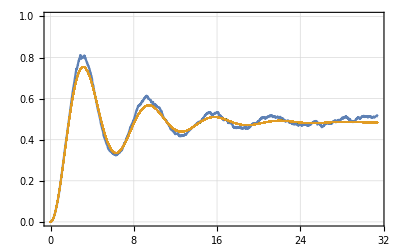

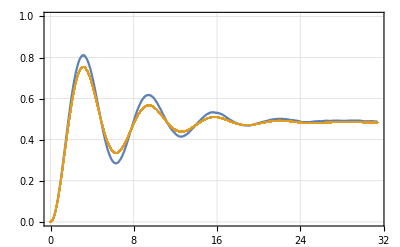

```mathematica
Show[MC10,denseP]
Show[MC50,denseP]
Show[MC250,denseP]
Show[MC1250,denseP]
```